```mathematica
Quit[]
```

## Load data

```mathematica
(* Load data first *)
Do[
cohomology[NN]=Import[NotebookDirectory[]<>"cohomology_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
MaxLevel[NN_] := Switch[NN,
2,25,
3,19,
4,15];
NumAllStatesUpToLevel[NN_,level_] := Total[#[[9]]&/@Select[cohomology[NN],#[[1]]<=level&]];
NumAllStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,9]];
NumMultiGravitonStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,10]];
```

```mathematica
(* Usage example *)
NumAllStates[2,{0,0,4,4,4},7]
NumMultiGravitonStates[2,{0,0,4,4,4},7]
```

1

0

## U(1) partition function

```mathematica
level=25;
ZU1sw[x_,a_,b_,u_,v_,w_]:=(a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b)) x
ZU1B[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]+ZU1sw[-x,a,b,-u,-v,-w])
ZU1F[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]-ZU1sw[-x,a,b,-u,-v,-w])

ZU1[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(ZU1B[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n ZU1F[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
ZU1reduced[x_]:=ZU1[1,x^3,x^3,x^2,x^2,x^2]
IU1reduced[x_]:=ZU1[-1,x^3,x^3,-x^2,-x^2,-x^2]
```

## Partition function

```mathematica
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
PermutationMultiplicity[charges_] := Length[Permutations[charges[[1;;2]]]]*Length[Permutations[charges[[3;;5]]]];
Index[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[3;;5]]) PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
NumAllStates[NN_,charges_] := Sum[ PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
Index[NN_,level_] := Sum[Index[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
NumAllStates[NN_,level_] := Sum[NumAllStates[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
Index[NN_] := Index[NN] = Series[(1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
NumAllStates[NN_] :=NumAllStates[NN] = Series[(1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UIndex[NN_] := UIndex[NN] = Series[IU1reduced[x] (1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UNumAllStates[NN_] := UNumAllStates[NN] = Series[ZU1reduced[x] (1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

```mathematica
UIndex[2]
```

1+3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+O[x]^26

```mathematica
Index[2]
```

1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25+O[x]^26

## Graviton partition function

```mathematica
level=25;
f[x_,a_,b_,u_,v_,w_]:=(1+ u)(1+ v)(1+  w)/(1-a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- u(1+ v)(1+ w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- v(1+  w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x v)/(1-x w)-1)-w/(1- a)/(1- b)((1+ x a)(1+x b)/(1-x w)-1)-a b x/(1- a)/(1- b)-((a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b))) x

fB[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]+f[-x,a,b,-u,-v,-w])/2
fF[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]-f[-x,a,b,-u,-v,-w])/2
Zgrav[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(fB[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n fF[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
Zgravreduced[x_]:=Zgrav[1,x^3,x^3,x^2,x^2,x^2]
Igravreduced[x_]:=Zgrav[-1,x^3,x^3,-x^2,-x^2,-x^2]

ZUgravreduced[x_]:=Series[ZU1reduced[x]Zgravreduced[x],{x,0,level}]
IUgravreduced[x_]:=Series[IU1reduced[x]Igravreduced[x],{x,0,level}]
```

```mathematica
ZUgravreduced[x]
IUgravreduced[x]
```

1+3 x^2+2 x^3+15 x^4+18 x^5+61 x^6+102 x^7+264 x^8+490 x^9+1107 x^10+2160 x^11+4574 x^12+9018 x^13+18375 x^14+36160 x^15+71931 x^16+140406 x^17+274534 x^18+530754 x^19+1023942 x^20+1960192 x^21+3739383 x^22+7091604 x^23+13396454 x^24+25183602 x^25+O[x]^26

1+3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+48 x^8-42 x^9+99 x^10-96 x^11+200 x^12-198 x^13+381 x^14-396 x^15+711 x^16-750 x^17+1278 x^18-1386 x^19+2256 x^20-2472 x^21+3879 x^22-4320 x^23+6564 x^24-7362 x^25+O[x]^26

## Tables

```mathematica
NN = 2;
StringReplace[Join[{{"Level","SU","SU Index","U", "U Index"}},Join[{Range[0,MaxLevel[NN]]},CoefficientList[{NumAllStates[NN],Index[NN],UNumAllStates[NN],UIndex[NN]},x]]//Transpose]//MatrixForm//TeXForm//ToString,{"\\\\"->"\\\\\\hline"}]
```

\left(
\begin{array}{ccccc}
 \text{Level} & \text{SU} & \text{SU Index} & \text{U} & \text{U Index} \\\hline
 0 & 1 & 1 & 1 & 1 \\\hline
 1 & 0 & 0 & 0 & 0 \\\hline
 2 & 0 & 0 & 3 & 3 \\\hline
 3 & 0 & 0 & 2 & -2 \\\hline
 4 & 6 & 6 & 15 & 9 \\\hline
 5 & 6 & -6 & 18 & -6 \\\hline
 6 & 9 & -7 & 51 & 11 \\\hline
 7 & 18 & 18 & 90 & -6 \\\hline
 8 & 30 & 6 & 195 & 9 \\\hline
 9 & 40 & -36 & 362 & 14 \\\hline
 10 & 66 & 6 & 699 & -21 \\\hline
 11 & 120 & 84 & 1308 & 36 \\\hline
 12 & 198 & -80 & 2431 & -17 \\\hline
 13 & 324 & -132 & 4434 & -18 \\\hline
 14 & 537 & 309 & 8046 & 114 \\\hline
 15 & 822 & -18 & 14346 & -194 \\\hline
 16 & 1257 & -567 & 25434 & 258 \\\hline
 17 & 1944 & 516 & 44544 & -168 \\\hline
 18 & 2959 & 613 & 77442 & -112 \\\hline
 19 & 4476 & -1392 & 133386 & 630 \\\hline
 20 & 6834 & -180 & 228021 & -1089 \\\hline
 21 & 10352 & 2884 & 386898 & 1130 \\\hline
 22 & 15540 & -1926 & 651843 & -273 \\\hline
 23 & 23406 & -4242 & 1091004 & -1632 \\\hline
 24 & 35076 & 7890 & 1814578 & 4104 \\\hline
 25 & 52020 & 792 & 2999724 & -5364 \\\hline
\end{array}
\right)

## Plots

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 1.5;
```

```mathematica
Do[
Export["/Users/yinhslin/git/bh/SU"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[NumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[Index[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["SU("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}},TicksStyle->Directive[Black,size]]];
Export["/Users/yinhslin/git/bh/U"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[UNumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[UIndex[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["U("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}}]];
,{NN,2,4}
]
```

## Load anomalous dimensions

```mathematica
(* Load data first *)
Do[
ad[NN]=Import[NotebookDirectory[]<>"ad_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
```

```mathematica
MaxLevel[NN_] := Switch[NN,
2,24,
3,17,
4,15];
OrganizeData[data_]:=Tally[Sort[Flatten[#[[9;;]]&/@data]]];
AD[NN_]:=ad[NN]//OrganizeData;
AD[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]//OrganizeData];
AD[NN_,charges_,degree_]:=AD[NN,charges,degree]=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&&#[[7]]==degree&]//OrganizeData];
ADUpToLevel[NN_,level_]:=Select[ad[NN],#[[1]]<=level&]//OrganizeData;
charges[level_]:=Flatten[#]&/@DeleteDuplicates[{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers]]
```

```mathematica
ad[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]];
adAll[NN_]:=adAll[NN]=Flatten[Table[ad[2,c],{l,4,MaxLevel[NN] },{c,charges[l]}],2];
adAll[2];
```

## characters

```mathematica
χsu2[m_][t_]:=(t^(1/2(2m+1))-t^(-1/2(2m+1)))/(t^(1/2)-t^(-1/2));
χsu3[m1_,m2_][t1_,t2_]:=t1^(m1+2m2)Sum[t1^(-3/2(k+l))(t1^((k-l+1)/2)t2^(-(k-l+1))-t1^(-(k-l+1)/2)t2^((k-l+1)))/(t1^(1/2)t2^-1-t1^(-1/2)t2),{k,m2,m1+m2},{l,0,m2}];
χ[EE_,JL_,JR_,q1_,q2_,q3_]:=Module[{s3,t2},Exp[-β EE-JL(ω1+ω2)-1/3(Δ1+Δ2+Δ3)(q1+q2+q3)]χsu2[JR][Exp[-(ω1-ω2)]]/(1-Exp[-β-ω1])/(1-Exp[-β-ω2])χsu3[q1-q2,q2-q3][Exp[-1/3(2Δ1-Δ2-Δ3)],Exp[-1/3(Δ1+Δ2-2Δ3)]](1+Exp[-1/2(β-ω1-ω2+ Δ1+ Δ2+ Δ3)])(1+Exp[-1/2(β+ω1+ω2- Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1+ω2- Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β+ω1+ω2+ Δ1- Δ2- Δ3)])
(1+Exp[-1/2(β+ω1-ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β-ω1+ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1+ Δ2- Δ3)])
];
fugacity={β->-2Log[t0],ω1->-2Log[a]-Log[t0],ω2->-2Log[b]-Log[t0],Δ1->-2Log[u],Δ2->-2Log[v],Δ3->-2Log[w]};
```

## Partition function

```mathematica
Z[L_,Δ_]:=Z[L,Δ]=Sum[(a b)^(Total[c]-d)(a/ b)^(c[[1]]-c[[2]])u^(c[[3]]-c[[4]]-c[[5]]+d)v^(-c[[3]]+c[[4]]-c[[5]]+d)w^(-c[[3]]-c[[4]]+c[[5]]+d)t0^l ed[[2]],{l,4,L},{c,charges[l]},{d,2,Total[c]},{ed,Select[AD[2,c,d],#[[1]]==Δ&]}]
```

```mathematica
L=24;
Δ=1.5;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[5/2,1/2,0,1/2,1/2,1/2]+χ[11/2,2/2,1/2,5/2,1/2,1/2]+χ[15/2,3/2,0,7/2,1/2,1/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
L=24;
Δ=0.47546;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[18/2,5/2,1/2,4/2,2/2,2/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
L=24;
Δ=0.75;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[13/2,3/2,0/2,3/2,3/2,1/2]+χ[17/2,5/2,0/2,5/2,1/2,1/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
primaryCharge[expr_]:=Module[{series,leadingLevel, exp},
series=Series[expr,{t0,0,24}];
leadingLevel=Min[Exponent[Normal[series],t0,List]];
exp=Exponent[Coefficient[series,t0^leadingLevel]//Normal//Expand//First,{a,b,u,v,w}];
{1/2(leadingLevel-(exp[[1]]+exp[[2]])/2),(exp[[1]]+exp[[2]])/4,(exp[[1]]-exp[[2]])/4,exp[[3]]/2,exp[[4]]/2,exp[[5]]/2}
]
primaries[expr_]:=Module[{p={},exponent,Z},
Z=expr;
While[((Series[Z,{t0,0,24}]//Normal)/.{t0->1,a->1,b->1,u->1,v->1,w->1})!=0,
exponent=primaryCharge[Z];
AppendTo[p,exponent];
Z=Z-Assuming[a>0&&b>0,Series[χ@@exponent/.fugacity//Simplify,{t0,0,24}]];
];
p
]
```

```mathematica
Do[
Print[{d,primaries[Z[24,d]]}];,
{d,DeleteCases[AD[2][[;;,1]],0]}]
```

{0.47546,{{9,5/2,1/2,2,1,1}}}

{0.75,{{13/2,3/2,0,3/2,3/2,1/2},{17/2,5/2,0,5/2,1/2,1/2}}}

{0.7804,{{7,2,1,1,1,1}}}

{0.82568,{{19/2,5/2,0,3/2,3/2,3/2}}}

{0.85411,{{19/2,5/2,1,5/2,3/2,1/2}}}

{0.8698,{{8,2,0,2,1,1}}}

{0.8871,{{19/2,2,1/2,7/2,3/2,1/2}}}

{0.93193,{{8,2,1,2,1,1}}}

{0.9693,{{19/2,5/2,1,7/2,1/2,1/2}}}

{0.97352,{{9,3,2,1,1,1}}}

{0.99563,{{19/2,5/2,0,3/2,3/2,3/2}}}

{1,{{11/2,3/2,0,3/2,1/2,1/2}}}

{1.00204,{{17/2,5/2,1,3/2,3/2,1/2}}}

{1.02761,{{15/2,2,1/2,3/2,3/2,1/2}}}

{1.03129,{{17/2,2,1/2,7/2,1/2,1/2}}}

{1.12361,{{19/2,5/2,0,5/2,3/2,1/2}}}

{1.125,{{6,3/2,1/2,1,1,1},{19/2,5/2,0,5/2,3/2,1/2}}}

{1.13339,{{9,2,1,3,1,1}}}

{1.14222,{{9,3,1,1,1,1}}}

{1.14276,{{9,5/2,3/2,2,1,1}}}

{1.22935,{{19/2,5/2,1,3/2,3/2,3/2}}}

{1.23226,{{17/2,2,3/2,3/2,3/2,3/2}}}

{1.23814,{{15/2,5/2,1,3/2,1/2,1/2}}}

{1.25826,{{9,2,0,2,2,1}}}

{1.2597,{{8,5/2,1/2,1,1,1}}}

{1.26106,{{19/2,2,1/2,9/2,1/2,1/2}}}

{1.29418,{{13/2,3/2,1,5/2,1/2,1/2}}}

{1.30931,{{8,5/2,3/2,1,1,1}}}

{1.31677,{{17/2,5/2,2,3/2,3/2,1/2}}}

{1.33443,{{19/2,2,3/2,9/2,1/2,1/2}}}

{1.34904,{{8,5/2,1/2,1,1,1}}}

{1.35441,{{17/2,5/2,2,5/2,1/2,1/2}}}

{1.35648,{{19/2,5/2,1,5/2,3/2,1/2}}}

{1.36018,{{19/2,5/2,1,7/2,1/2,1/2}}}

{1.3699,{{19/2,2,1/2,5/2,3/2,3/2}}}

{1.36991,{{7,3/2,3/2,2,1,1},{7,2,1,2,1,0}}}

{1.38269,{{10,2,1,4,1,1}}}

{1.40253,{{10,2,0,4,1,1}}}

{1.40876,{{10,2,2,4,1,1}}}

{1.41427,{{17/2,2,1/2,5/2,3/2,1/2}}}

{1.41443,{{19/2,5/2,2,3/2,3/2,3/2}}}

{1.42432,{{9,5/2,5/2,2,1,1},{9,3,2,2,1,0}}}

{1.43633,{{9,3,1,1,1,1}}}

{1.43756,{{17/2,5/2,0,5/2,1/2,1/2}}}

{1.44167,{{19/2,2,3/2,7/2,3/2,1/2}}}

{1.44713,{{17/2,3/2,1,9/2,1/2,1/2}}}

{1.46949,{{17/2,2,3/2,7/2,1/2,1/2}}}

{1.49385,{{17/2,3,3/2,3/2,1/2,1/2}}}

{1.5,{{5/2,1/2,0,1/2,1/2,1/2},{11/2,1,1/2,5/2,1/2,1/2},{15/2,3/2,0,7/2,1/2,1/2}}}

{1.5004,{{17/2,5/2,1,3/2,3/2,1/2}}}

{1.5119,{{9,5/2,1/2,2,1,1}}}

{1.5197,{{9,5/2,1/2,3,1,0}}}

{1.54223,{{8,2,2,2,1,1},{8,5/2,3/2,2,1,0}}}

{1.57578,{{9,5/2,3/2,2,1,1}}}

{1.58786,{{19/2,5/2,1,5/2,3/2,1/2}}}

{1.58911,{{15/2,2,3/2,5/2,1/2,1/2}}}

{1.59235,{{19/2,2,1/2,5/2,5/2,1/2}}}

{1.5954,{{10,2,1,3,2,1}}}

{1.6107,{{9,5/2,1/2,2,2,0}}}

{1.6198,{{17/2,3/2,0,7/2,3/2,1/2}}}

{1.63779,{{9,2,0,3,1,1}}}

{1.63811,{{13/2,2,1/2,3/2,1/2,1/2}}}

{1.64296,{{9,2,1,3,1,1}}}

{1.64409,{{19/2,5/2,0,3/2,3/2,3/2}}}

{1.64784,{{17/2,5/2,1,5/2,1/2,1/2}}}

{1.65368,{{19/2,5/2,1,7/2,1/2,1/2}}}

{1.67778,{{19/2,2,1/2,7/2,3/2,1/2}}}

{1.68837,{{19/2,5/2,2,5/2,3/2,1/2}}}

{1.73743,{{9,5/2,1/2,2,1,1}}}

{1.74754,{{15/2,2,1/2,5/2,1/2,1/2}}}

{1.74977,{{17/2,2,1/2,5/2,3/2,1/2}}}

{1.77748,{{8,2,1,2,1,1}}}

{1.79696,{{9,3,1,2,1,0}}}

{1.80582,{{9,2,1,3,1,1}}}

{1.8097,{{8,3/2,1/2,3,1,1}}}

{1.82585,{{9,2,1,2,2,1}}}

{1.84172,{{17/2,3,3/2,3/2,1/2,1/2}}}

{1.8553,{{19/2,2,3/2,5/2,3/2,3/2}}}

{1.87442,{{9,2,1,2,2,1}}}

{1.875,{{9/2,1,1/2,3/2,1/2,1/2},{9,2,0,4,1,0}}}

{1.87568,{{7,3/2,1/2,2,1,1}}}

{1.88392,{{19/2,5/2,0,5/2,3/2,1/2}}}

{1.89869,{{15/2,2,3/2,3/2,3/2,1/2}}}

{1.90035,{{10,2,1,4,1,1}}}

{1.90812,{{15/2,3/2,1,3/2,3/2,3/2}}}

{1.90977,{{17/2,5/2,0,3/2,3/2,1/2}}}

{1.9108,{{9,5/2,1/2,2,1,1}}}

{1.91527,{{9,3,2,1,1,1}}}

{1.92834,{{19/2,2,1/2,5/2,3/2,3/2}}}

{1.93237,{{19/2,5/2,2,3/2,3/2,3/2}}}

{1.93294,{{17/2,5/2,2,5/2,1/2,1/2}}}

{1.95366,{{9,5/2,3/2,2,1,1}}}

$Aborted

```mathematica
AD[2]
```

{{0,17990},{0.47546,26},{0.75,1302},{0.7804,610},{0.82568,2},{0.85411,12},{0.8698,210},{0.8871,92},{0.93193,548},{0.9693,12},{0.97352,6},{0.99563,2},{1,2104},{1.00204,110},{1.02761,698},{1.03129,490},{1.12361,6},{1.125,1196},{1.13339,182},{1.14222,4},{1.14276,44},{1.22935,4},{1.23226,138},{1.23814,548},{1.25826,44},{1.2597,78},{1.26106,80},{1.29418,5998},{1.30931,138},{1.31677,168},{1.33443,136},{1.34904,78},{1.35441,278},{1.35648,12},{1.36018,12},{1.3699,26},{1.36991,6866},{1.38269,12},{1.40253,6},{1.40876,18},{1.41427,448},{1.41443,6},{1.42432,80},{1.43633,4},{1.43756,74},{1.44167,156},{1.44713,1988},{1.46949,860},{1.49385,44},{1.5,13680},{1.5004,110},{1.5119,26},{1.5197,92},{1.54223,1630},{1.57578,44},{1.58786,12},{1.58911,2194},{1.59235,40},{1.5954,12},{1.6107,40},{1.6198,844},{1.63779,74},{1.63811,1676},{1.64296,182},{1.64409,2},{1.64784,182},{1.65368,12},{1.67778,92},{1.68837,18},{1.73743,26},{1.74754,1224},{1.74977,448},{1.77748,548},{1.79696,12},{1.80582,182},{1.8097,1224},{1.82585,110},{1.84172,44},{1.8553,44},{1.87442,110},{1.875,7792},{1.87568,1676},{1.88392,6},{1.89869,1254},{1.90035,12},{1.90812,610},{1.90977,44},{1.9108,26},{1.91527,6},{1.92834,26},{1.93237,6},{1.93294,278},{1.95366,44},{1.9631,28},{1.98178,4},{1.98647,156},{2,1042},{2.00583,6},{2.02033,12},{2.02473,6},{2.03041,6},{2.04127,236},{2.05784,786},{2.06126,210},{2.07885,6},{2.07895,18},{2.07968,434},{2.0801,490},{2.08207,26},{2.08333,3434},{2.08995,18},{2.11878,1468},{2.12093,12},{2.12255,26},{2.12566,490},{2.12886,44},{2.16667,4254},{2.1875,3060},{2.19496,1420},{2.19961,448},{2.21033,12},{2.21035,1988},{2.23363,548},{2.23639,26},{2.24378,182},{2.24524,12},{2.24896,6},{2.25,19842},{2.25334,44},{2.25902,44},{2.26117,12},{2.26521,6},{2.27399,18},{2.28331,138},{2.28466,78},{2.29716,12},{2.30086,182},{2.30258,12},{2.3058,698},{2.31063,78},{2.32055,18},{2.3255,1224},{2.32744,12},{2.32765,80},{2.34122,4},{2.34439,1224},{2.34779,18},{2.36433,136},{2.36571,952},{2.38691,548},{2.39008,12},{2.40342,4},{2.4189,3806},{2.42083,62},{2.42332,26},{2.43241,2},{2.43263,6},{2.43415,44},{2.43448,18},{2.44767,4},{2.44822,68},{2.44947,4},{2.45,948},{2.46782,4},{2.47855,1630},{2.5,21272},{2.53043,74},{2.54687,5998},{2.55337,110},{2.55644,80},{2.55848,92},{2.56387,44},{2.58601,80},{2.59139,18},{2.5966,12},{2.60415,12},{2.60639,6},{2.625,8572},{2.62779,110},{2.63934,182},{2.65687,278},{2.66885,12},{2.68047,18},{2.6843,138},{2.68996,210},{2.69427,448},{2.70323,92},{2.71245,18},{2.71786,8},{2.72099,110},{2.75,452},{2.75781,610},{2.75904,26},{2.75917,2},{2.7593,12},{2.76196,6},{2.77083,364},{2.77765,860},{2.78234,2},{2.78589,2194},{2.80855,26},{2.81488,12},{2.82103,548},{2.83333,490},{2.83466,40},{2.8375,844},{2.84413,18},{2.85576,1202},{2.86955,1254},{2.875,1396},{2.88829,78},{2.88928,448},{2.9134,110},{2.92382,490},{2.9375,138},{2.95819,28},{2.95973,548},{2.96027,246},{2.96243,74},{2.96737,4},{2.9695,12},{2.97858,1468},{2.98021,182},{2.98152,6},{2.9843,156},{2.98443,44},{2.98534,6},{3,5298},{3.01195,78},{3.01478,156},{3.01924,12},{3.02083,2},{3.02154,26},{3.02274,44},{3.0294,80},{3.03004,4},{3.03553,138},{3.04167,40},{3.04736,6},{3.04859,80},{3.05486,434},{3.07117,12},{3.075,4},{3.07845,182},{3.08296,92},{3.09413,6910},{3.10395,92},{3.10431,12},{3.11716,182},{3.11853,1676},{3.125,26},{3.14454,78},{3.15302,12},{3.15901,80},{3.16096,44},{3.16667,432},{3.17083,8},{3.17493,44},{3.18461,18},{3.1884,6},{3.18995,26},{3.19334,26},{3.19344,608},{3.21391,12},{3.21783,110},{3.2213,448},{3.22179,2},{3.22197,136},{3.23447,4},{3.23755,44},{3.23847,2},{3.23994,548},{3.25,12862},{3.27345,110},{3.27914,6},{3.28755,4},{3.30141,44},{3.30979,182},{3.31023,40},{3.32078,26},{3.32755,6},{3.33333,44},{3.34027,44},{3.34981,80},{3.35746,698},{3.363,26},{3.36458,4},{3.36474,4},{3.37195,6},{3.375,4856},{3.37601,12},{3.38561,1254},{3.39249,1988},{3.39547,26},{3.40811,12},{3.40821,210},{3.41886,2},{3.42176,6866},{3.45406,12},{3.45833,6},{3.46727,4},{3.46763,18},{3.47438,6},{3.48814,448},{3.5,9240},{3.5156,44},{3.51692,12},{3.51706,6},{3.52014,138},{3.54167,448},{3.54779,4},{3.55197,110},{3.55206,92},{3.55431,12},{3.55599,548},{3.55971,110},{3.56296,44},{3.58223,182},{3.58726,6},{3.59613,4},{3.59648,2},{3.59724,236},{3.61189,1676},{3.61483,182},{3.64343,32},{3.64602,182},{3.65036,490},{3.65322,6},{3.6554,74},{3.66135,26},{3.66875,12},{3.6689,156},{3.6709,138},{3.67646,786},{3.67892,2},{3.68452,4},{3.68798,12},{3.69395,26},{3.69788,12},{3.70188,548},{3.70729,12},{3.71291,44},{3.71955,278},{3.72783,610},{3.74298,6},{3.74976,12},{3.75,12808},{3.75314,6},{3.7653,18},{3.7753,12},{3.78583,6},{3.78994,1224},{3.80039,448},{3.82985,12},{3.83281,448},{3.83598,110},{3.83674,92},{3.83964,6},{3.8426,6},{3.84281,6},{3.8518,44},{3.85197,2},{3.85508,26},{3.85692,92},{3.86722,36},{3.87273,44},{3.875,80},{3.87845,610},{3.8802,210},{3.88166,26},{3.8821,210},{3.89786,4},{3.90654,110},{3.90921,40},{3.91028,6},{3.91474,12},{3.91667,4},{3.92778,92},{3.93258,210},{3.93745,18},{3.94361,74},{3.94656,26},{3.947,182},{3.95348,786},{3.96381,80},{3.96579,44},{3.96791,12},{3.97223,4},{3.97791,26},{3.98809,548},{3.98965,698},{3.99736,6},{3.9975,18},{3.99831,6},{4,1508},{4.01117,156},{4.01973,40},{4.0208,12},{4.02089,1630},{4.02314,44},{4.02482,110},{4.04244,6},{4.04317,4},{4.05196,1224},{4.05568,78},{4.05823,168},{4.06113,12},{4.07438,4},{4.09179,12},{4.09413,198},{4.10171,138},{4.10508,78},{4.11662,110},{4.12421,74},{4.125,376},{4.13566,12},{4.13844,1516},{4.15896,5998},{4.17245,1676},{4.18477,182},{4.18917,952},{4.21028,2},{4.21922,92},{4.22098,92},{4.22764,4},{4.24173,26},{4.24455,138},{4.25,10278},{4.26064,12},{4.26215,6},{4.28177,18},{4.2862,12},{4.29613,18},{4.30177,44},{4.30801,6},{4.32161,28},{4.32379,434},{4.32611,6},{4.32863,182},{4.32977,12},{4.34344,18},{4.34585,80},{4.3508,698},{4.35144,548},{4.35647,44},{4.36659,78},{4.36872,78},{4.375,6640},{4.37812,448},{4.38601,12},{4.38946,548},{4.39435,44},{4.3958,18},{4.39955,44},{4.40129,182},{4.40245,40},{4.40797,2},{4.41454,4},{4.43097,12},{4.44235,110},{4.44298,188},{4.44538,448},{4.45009,40},{4.45124,12},{4.45181,6},{4.46021,6},{4.46766,2},{4.47409,44},{4.49542,4},{4.49593,136},{4.5,14874},{4.51679,4},{4.52468,156},{4.52816,236},{4.53035,110},{4.53095,182},{4.53462,6},{4.53528,6},{4.54373,12},{4.54759,4},{4.55159,44},{4.55382,182},{4.55443,74},{4.56096,12},{4.57991,26},{4.59524,92},{4.60762,44},{4.61452,6},{4.625,26},{4.6302,844},{4.63962,210},{4.64709,26},{4.64764,4},{4.65135,92},{4.65207,40},{4.65729,26},{4.65934,12},{4.67198,12},{4.67352,490},{4.67919,6},{4.68573,80},{4.68924,26},{4.69945,12},{4.7134,74},{4.71356,6},{4.71464,44},{4.71751,44},{4.7225,2},{4.72443,6},{4.74209,44},{4.74222,6},{4.74377,6},{4.74777,3806},{4.75,1944},{4.75073,448},{4.7534,182},{4.75613,110},{4.76166,18},{4.76282,1254},{4.76296,44},{4.78182,26},{4.78317,12},{4.78365,12},{4.78591,12},{4.78671,1224},{4.79362,6},{4.80327,12},{4.80504,1420},{4.80726,44},{4.80861,6},{4.81771,18},{4.82052,6},{4.83094,12},{4.86137,110},{4.875,1056},{4.88903,26},{4.89038,32},{4.8958,156},{4.8987,860},{4.90943,4},{4.93692,12},{4.94413,12},{4.94431,4},{4.98699,40},{4.99508,12},{5,3808},{5.00795,40},{5.03175,6},{5.0415,4},{5.04269,448},{5.04435,548},{5.0597,92},{5.06225,6},{5.06931,1468},{5.07027,6},{5.08363,182},{5.08467,138},{5.08547,44},{5.08575,26},{5.10029,12},{5.10349,110},{5.125,1734},{5.1348,12},{5.13623,278},{5.15986,18},{5.16553,92},{5.18403,12},{5.19313,26},{5.19805,12},{5.23414,548},{5.25,924},{5.25128,12},{5.25285,12},{5.25985,44},{5.26925,1224},{5.27018,26},{5.28072,610},{5.28843,18},{5.28882,6},{5.30069,40},{5.3068,12},{5.31091,1202},{5.31106,12},{5.31429,110},{5.31485,26},{5.32158,490},{5.3297,92},{5.33738,188},{5.34747,6},{5.38624,44},{5.39556,786},{5.39907,74},{5.40587,18},{5.42131,6},{5.42849,12},{5.43429,80},{5.45137,448},{5.45472,6},{5.46081,156},{5.461,12},{5.4662,2},{5.46829,182},{5.5,8962},{5.51035,698},{5.52538,26},{5.53494,6},{5.55078,4},{5.55641,12},{5.57729,12},{5.58429,78},{5.5846,26},{5.59599,18},{5.60332,12},{5.60382,12},{5.61069,92},{5.61631,6},{5.625,1420},{5.65085,182},{5.65587,6910},{5.66805,4},{5.70238,952},{5.70815,44},{5.71845,68},{5.73783,80},{5.74043,416},{5.75,1688},{5.76438,12},{5.80554,92},{5.8152,2},{5.81898,448},{5.82592,18},{5.82856,110},{5.83092,6},{5.84573,18},{5.87132,6},{5.87252,92},{5.875,144},{5.88278,36},{5.89804,12},{5.9047,156},{5.92869,12},{5.93536,6},{5.94366,490},{5.96707,182},{5.97307,26},{6,898},{6.02062,44},{6.02111,4},{6.0316,2},{6.03644,6},{6.04703,32},{6.08505,448},{6.08972,6},{6.10203,12},{6.10521,92},{6.11669,1988},{6.125,3660},{6.1363,188},{6.15072,40},{6.16402,12},{6.17649,110},{6.18982,4},{6.19561,6},{6.2334,12},{6.25,44},{6.25007,26},{6.29456,6},{6.31552,18},{6.32396,12},{6.33856,168},{6.34139,6},{6.36593,110},{6.37028,2},{6.37933,44},{6.40694,182},{6.41681,4},{6.42404,12},{6.42794,210},{6.44115,44},{6.44315,12},{6.44496,448},{6.4559,80},{6.4611,40},{6.47322,608},{6.5,6938},{6.50494,18},{6.53973,246},{6.58114,2},{6.63126,12},{6.63373,12},{6.64204,182},{6.65587,198},{6.65838,12},{6.66726,6},{6.75,210},{6.8147,2},{6.82374,32},{6.84183,92},{6.85738,92},{6.875,106},{6.90941,952},{6.91966,26},{6.9289,4},{6.96825,6},{7,4192},{7.01616,6},{7.02598,80},{7.02687,6},{7.05336,110},{7.09752,40},{7.10129,92},{7.13763,12},{7.18529,26},{7.22398,32},{7.23784,448},{7.25,562},{7.30473,40},{7.33139,44},{7.375,246},{7.4084,12},{7.41036,6},{7.4226,12},{7.43096,6},{7.4698,12},{7.5,126},{7.52339,156},{7.52475,26},{7.59861,6},{7.60477,6},{7.61156,1516},{7.65929,6},{7.66144,168},{7.74224,12},{7.7448,92},{7.75,44},{7.79817,12},{7.84796,12},{7.875,916},{7.92624,416},{7.94965,4},{8,562},{8.08383,4},{8.09044,28},{8.17726,40},{8.22903,12},{8.25,6},{8.28536,44},{8.33866,182},{8.34413,16},{8.375,40},{8.5,998},{8.52378,92},{8.54997,26},{8.56486,40},{8.75,502},{9,782},{9.05504,448},{9.06042,32},{9.125,12},{9.12624,6},{9.25,168},{9.26278,6},{9.40139,6},{9.46329,12},{9.58274,6},{9.64436,32},{9.75,132},{9.99812,4},{10,366},{10.5,164},{10.625,26},{10.7552,92},{10.875,6},{10.9059,16},{12,74},{13,16},{15,2}}

## Statistics

```mathematica
Gap[tmp_]:=If[Length[tmp]==0,0,If[tmp[[1,1]]==0,If[Length[tmp]==1,0,tmp[[2,1]]],tmp[[1,1]]]];
Gap[NN_,charges_]:=Module[{tmp=AD[NN,charges]},Gap[tmp]];
GapUpToLevel[NN_,level_]:=Module[{tmp=ADUpToLevel[NN,level]},Gap[tmp]];
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
Stats[NN_,charges_]:=Module[{ad=AD[NN,charges],sum=0,dim=0,sumNoneBPS=0,dimNoneBPS=0},
Do[sum+=i[[1]]*i[[2]];dim+=i[[2]];
If[i[[1]]>0,sumNoneBPS+=i[[1]]*i[[2]];dimNoneBPS+=i[[2]]];
,{i,ad}];
{dim,If[dim==0,0,sum/dim],dimNoneBPS,If[dimNoneBPS==0,0,sumNoneBPS/dimNoneBPS],Gap[ad]}
];
```

```mathematica
chargeList=Flatten[Table[ChargeList[l],{l,4,24}],1];
stats=Stats[2,#]&/@ chargeList;
```

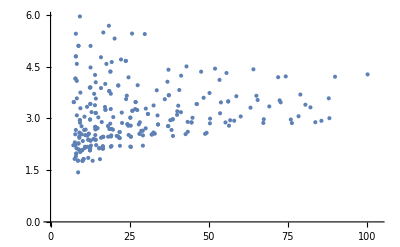

```mathematica
statsX=Select[stats,#[[1]]>=50&];
ListPlot[{Sqrt[#[[1]]],#[[2]]}&/@statsX]
```

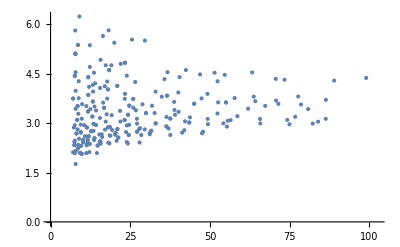

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{Sqrt[#[[3]]],#[[4]]}&/@statsX]
```

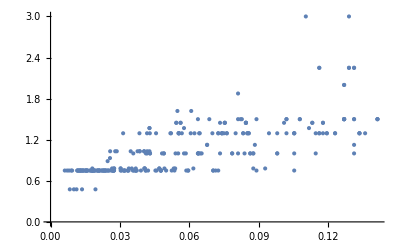

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{1/Sqrt[#[[3]]],#[[5]]}&/@statsX]
```

## Sanity Check

```mathematica
(* Usage example *)
ADUpToLevel[2,24][[1;;5]]
ADUpToLevel[3,16][[1;;5]]
ADUpToLevel[4,15][[1;;5]]
```

{{0,17990},{0.47546,26},{0.75,1302},{0.7804,610},{0.82568,2}}

{{0,2544},{0.83324,8},{0.85942,72},{1.03884,4},{1.1305,4}}

{{0,2051},{0.88412,10},{1.27864,6},{1.29666,16},{1.31934,6}}

```mathematica
(* Sanity check *)
NumAllStatesUpToLevel[2,24]
NumAllStatesUpToLevel[3,16]
NumAllStatesUpToLevel[4,15]
```

17990

2544

2051